# 1. naloga

```mathematica
izraz=((x^5-2 x^2+3x+4)/(x^5-2x-1))
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
izraz /. x-> 1
ReplaceAll[izraz,x->1]
izraz /. x->2
izraz /.{{x->1}, {x->2}, {x->3}, {x->4}, {x->5}}
izraz /. x->{1,2,3,4,5}
```

-3

-3

34/27

{-3,34/27,119/118,144/145,1547/1557}

{-3,34/27,119/118,144/145,1547/1557}

```mathematica
f[x_]:=(x^5-2 x^2+3x+4)/(x^5-2x-1)
```

```mathematica
Table[f[x],{x,1,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
f[1]
```

-3

# 2. naloga

```mathematica
sez={10,20,30,40,50,60,70}
```

{10,20,30,40,50,60,70}

```mathematica
sez=Table[x*10,{x,7}]
```

{10,20,30,40,50,60,70}

```mathematica
Take[sez,3]
```

{10,20,30}

```mathematica
Drop[sez,-4]
```

{10,20,30}

```mathematica
Take[sez,-2]
```

{60,70}

```mathematica
Part[sez,{6,7}]
```

{60,70}

```mathematica
sez[[{6,7}]]
```

{60,70}

```mathematica
Range[20,40,10]
```

{20,30,40}

```mathematica
Take[sez,{2,4}]
```

{20,30,40}

```mathematica
Part[sez,{2,3,5}]
```

{20,30,50}

```mathematica
Drop[sez,{4,5}]
```

{10,20,30,60,70}

# 3. naloga

```mathematica
ClearAll[x,a]
```

```mathematica
sez={x^6,x^2,a}
```

{x^6,x^2,a}

```mathematica
sez /. x->3
```

{729,9,a}

```mathematica
sez /.x->x^2
```

{x^12,x^4,a}

```mathematica
sez /. x->x
```

{x^6,x^2,a}

```mathematica
sez /.x->{1,2,3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez /. {x->3,a->x}
```

{729,9,x}

```mathematica
sez //. {x->3,a->x}
```

{729,9,3}

```mathematica
ReplaceRepeated[sez,{x->3,a->x}]
```

{729,9,3}

# 4. naloga

```mathematica
D[x^5+4x^3-9,x]/. x->{1,5}
```

{17,3425}

```mathematica
D[ⅇ^(x^(1/4)),x]/.x->{1,2}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

```mathematica
FullSimplify[D[Abs[x+1],x],x∈Reals]
```

Sign[1+x]

```mathematica
D[ax^2+3b,x]/.x->{1,2}
```

{2 a,4 a}

# 5. naloga

```mathematica
narisi[x0_] :=Module[{k0,n0,t},
```

```mathematica
x0=7;
k0=D[f[x],x]/.x->x0;
n0=n/.First[Solve[f[x0]=k0*x0+n,n]];
```

```mathematica
t[x_]:=k0*x0+n;
```

```mathematica
f[x_]:=x^3Log[4x+5];
```

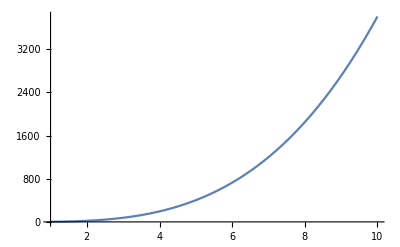

```mathematica
Plot[{{f[x],t[x]}},{x,1,10}]
]
```

```mathematica
x0=5
```

5

```mathematica
f[x0]
```

125 Log[25]

```mathematica
k0=D[f[x],x]/.x->x0
```

20+75 Log[25]

```mathematica
Solve[f[x0]=k0*x0+n,n]
```

# 7. naloga

```mathematica
izraz=(x^2-1)/(x^2-4)
```

(-1+x^2)/(-4+x^2)

```mathematica
Denominator[izraz]
```

-4+x^2

```mathematica
Solve[1/izraz=0,x]
```